-state viscosity waveNumbers^2

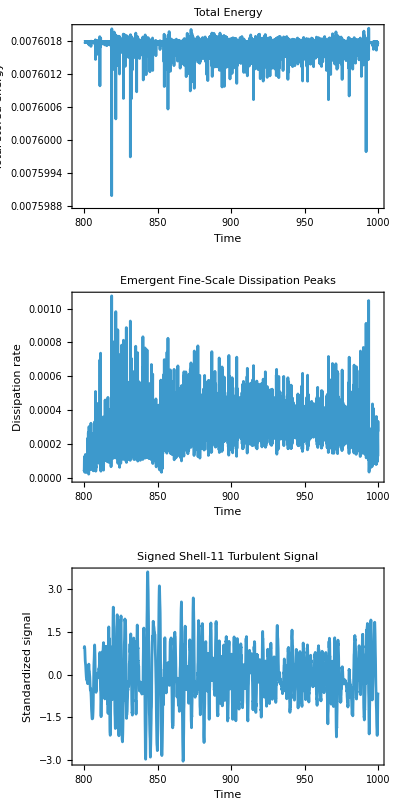

```mathematica
ClearAll[sabraNonlinearTerm,sabraRightHandSide,GenerateSabraTurbulence];

(*Conservative nonlinear interscale interaction*)

sabraNonlinearTerm[state_List,waveNumbers_List,coefficients_List]:=Module[{shellCount=Length[state],a=coefficients[[1]],b=coefficients[[2]],c=coefficients[[3]]},Table[I (If[shell<=shellCount-2,a waveNumbers[[shell+1]] state[[shell+2]] Conjugate[state[[shell+1]]],0.]+If[2<=shell<=shellCount-1,b waveNumbers[[shell]] state[[shell+1]] Conjugate[state[[shell-1]]],0.]-If[shell>=3,c waveNumbers[[shell-1]] state[[shell-1]] state[[shell-2]],0.]),{shell,shellCount}]];


(*Full dynamics:nonlinear transfer+fine-scale viscosity+coarse forcing*)

sabraRightHandSide[state_List,waveNumbers_List,viscosity_?NumericQ,coefficients_List,forcing_List]:=sabraNonlinearTerm[state,waveNumbers,coefficients]
-viscosity waveNumbers^2 state
+forcing;
Options[GenerateSabraTurbulence]={"ShellCount"->16,"ShellRatio"->2.,"BaseWaveNumber"->1./16.,"Coefficients"->{1.,-0.5,-0.5},"Viscosity"->1.*^-7,"ForcingShell"->1,"ForcingAmplitude"->0.005,"InitialAmplitude"->0.02,"BurnInTime"->500.,"SampleDuration"->500.,"SampleInterval"->0.05,"MaximumStepSize"->0.02,"ObservableShell"->Automatic};


GenerateSabraTurbulence[seed_Integer,OptionsPattern[]]:=Module[{shellCount,shellRatio,baseWaveNumber,coefficients,viscosity,forcingShell,forcingAmplitude,forcing,initialAmplitude,phases,amplitudeJitter,initialState,burnInTime,sampleDuration,sampleInterval,maximumStepSize,totalTime,waveNumbers,shellFunctions,stateVector,equations,initialConditions,solutionFunctions,sampleTimes,sampledStates,shellEnergy,totalEnergy,dissipationByShell,totalDissipation,relativeDissipation,conditionalScale,instantaneousInjection,observableShell,rawSignedSignal,signedSignal,nonlinearEnergyRate},shellCount=OptionValue["ShellCount"];
shellRatio=OptionValue["ShellRatio"];
baseWaveNumber=OptionValue["BaseWaveNumber"];
coefficients=N@OptionValue["Coefficients"];
viscosity=N@OptionValue["Viscosity"];
forcingShell=OptionValue["ForcingShell"];
forcingAmplitude=N@OptionValue["ForcingAmplitude"];
initialAmplitude=N@OptionValue["InitialAmplitude"];
burnInTime=N@OptionValue["BurnInTime"];
sampleDuration=N@OptionValue["SampleDuration"];
sampleInterval=N@OptionValue["SampleInterval"];
maximumStepSize=N@OptionValue["MaximumStepSize"];
totalTime=burnInTime+sampleDuration;
(*Logarithmically separated scales*)waveNumbers=baseWaveNumber shellRatio^Range[0,shellCount-1];
(*Energy-conserving coefficient condition*)If[Abs[Total[coefficients]]>10^-12,Return[Failure["InvalidSabraCoefficients",<|"Message"->"The coefficients must satisfy a + b + c == 0.","Coefficients"->coefficients,"CoefficientSum"->Total[coefficients]|>]]];
(*Constant forcing only on a coarse shell*)forcing=ConstantArray[0.+0. I,shellCount];
forcing[[forcingShell]]=forcingAmplitude (1.+I);
(*The seed determines only the initial condition.Evolution after t=0 is deterministic.*)BlockRandom[SeedRandom[seed,Method->"MersenneTwister"];
phases=RandomReal[{0.,2. Pi},shellCount];
amplitudeJitter=Exp[0.15 RandomVariate[NormalDistribution[0.,1.],shellCount]];];
initialState=initialAmplitude waveNumbers^(-1./3.) amplitudeJitter Exp[I phases];
(*Verify the nonlinear term itself conserves energy*)nonlinearEnergyRate=2. Re[Total[Conjugate[initialState] sabraNonlinearTerm[initialState,waveNumbers,coefficients]]];
(*Independent symbols prevent contamination from an old notebook*)shellFunctions=Table[Unique["sabraVelocity$"],shellCount];
stateVector=Through[shellFunctions[t]];
equations=Thread[D[stateVector,t]==sabraRightHandSide[stateVector,waveNumbers,viscosity,coefficients,forcing]];
initialConditions=Thread[(stateVector/. t->0.)==initialState];
solutionFunctions=NDSolveValue[Join[equations,initialConditions],shellFunctions,{t,0.,totalTime},Method->"StiffnessSwitching",MaxStepSize->maximumStepSize,AccuracyGoal->8,PrecisionGoal->8];
(*Burn-in is discarded*)sampleTimes=Range[burnInTime,totalTime,sampleInterval];
sampledStates=Transpose[(#/@sampleTimes)&/@solutionFunctions];
shellEnergy=Abs[sampledStates]^2;
totalEnergy=Total/@shellEnergy;
dissipationByShell=(2. viscosity waveNumbers^2 Abs[#]^2)&/@sampledStates;
totalDissipation=Total/@dissipationByShell;
relativeDissipation=totalDissipation/Mean[totalDissipation];
conditionalScale=Sqrt[relativeDissipation];
instantaneousInjection=(2. Re[Total[Conjugate[#] forcing]])&/@sampledStates;
observableShell=Replace[OptionValue["ObservableShell"],Automatic->Max[3,Round[0.70 shellCount]]];
observableShell=Clip[observableShell,{1,shellCount}];
rawSignedSignal=Re[sampledStates[[All,observableShell]]];
signedSignal=(rawSignedSignal-Mean[rawSignedSignal])/StandardDeviation[rawSignedSignal];
<|"Stage"->"EndogenousSabraMultiscaleTurbulence","Seed"->seed,"Times"->sampleTimes,"WaveNumbers"->waveNumbers,"Forcing"->forcing,"InitialState"->initialState,"ShellVelocity"->sampledStates,"ShellEnergy"->shellEnergy,"TotalEnergy"->totalEnergy,"DissipationByShell"->dissipationByShell,"TotalDissipation"->totalDissipation,"RelativeDissipation"->relativeDissipation,"ConditionalScale"->conditionalScale,"InstantaneousEnergyInjection"->instantaneousInjection,"ObservableShell"->observableShell,"SignedTurbulentSignal"->signedSignal,"Checks"-><|"CoefficientSum"->Total[coefficients],"InitialNonlinearEnergyRate"->Chop[nonlinearEnergyRate],"ExpectedNonlinearEnergyRate"->0.|>,"Parameters"-><|"ShellCount"->shellCount,"ShellRatio"->shellRatio,"BaseWaveNumber"->baseWaveNumber,"Coefficients"->coefficients,"Viscosity"->viscosity,"ForcingShell"->forcingShell,"ForcingAmplitude"->forcingAmplitude,"BurnInTime"->burnInTime,"SampleDuration"->sampleDuration,"SampleInterval"->sampleInterval,"MaximumStepSize"->maximumStepSize|>|>];
sabraSeed=20260817;

sabraCore=GenerateSabraTurbulence[sabraSeed];
Dataset[sabraCore["Checks"]]
sabraTimes=sabraCore["Times"];

sabraPlotCount=Min[4000,Length[sabraTimes]];

sabraPlotTimes=Take[sabraTimes,-sabraPlotCount];


sabraEnergyPlot=ListLinePlot[Transpose[{sabraPlotTimes,Take[sabraCore["TotalEnergy"],-sabraPlotCount]}],Frame->True,FrameLabel->{"Time","Total stored energy"},PlotLabel->"Total Energy",PlotRange->All,ImageSize->Large];


sabraDissipationPlot=ListLinePlot[Transpose[{sabraPlotTimes,Take[sabraCore["TotalDissipation"],-sabraPlotCount]}],Frame->True,FrameLabel->{"Time","Dissipation rate"},PlotLabel->"Emergent Fine-Scale Dissipation Peaks",PlotRange->All,ImageSize->Large];


sabraSignalPlot=ListLinePlot[Transpose[{sabraPlotTimes,Take[sabraCore["SignedTurbulentSignal"],-sabraPlotCount]}],Frame->True,FrameLabel->{"Time","Standardized signal"},PlotLabel->Row[{"Signed Shell-",sabraCore["ObservableShell"]," Turbulent Signal"}],PlotRange->All,ImageSize->Large];


GraphicsColumn[{sabraEnergyPlot,sabraDissipationPlot,sabraSignalPlot}]
```

```mathematica
(*Preserve the naturally realized sample mean.Normalize magnitude without sample-centering.*)sabraRawSignedSignal=Re[sabraCore["ShellVelocity"][[All,sabraCore["ObservableShell"]]]];

sabraSignedSignalRMS=Sqrt[Mean[sabraRawSignedSignal^2]];

sabraSignedTurbulentSignal=sabraRawSignedSignal/sabraSignedSignalRMS;


sabraCore=Join[sabraCore,<|"RawSignedTurbulentSignal"->sabraRawSignedSignal,"SignedSignalRMS"->sabraSignedSignalRMS,"SignedTurbulentSignal"->sabraSignedTurbulentSignal|>];
sabraEnergyDriftRate=(Last[sabraCore["TotalEnergy"]]-First[sabraCore["TotalEnergy"]])/(Last[sabraCore["Times"]]-First[sabraCore["Times"]]);


sabraMeanPowerImbalance=Mean[sabraCore["InstantaneousEnergyInjection"]-sabraCore["TotalDissipation"]];


sabraEnergyBalanceResidual=sabraEnergyDriftRate-sabraMeanPowerImbalance;


sabraRelativeBalanceResidual=Abs[sabraEnergyBalanceResidual]/Max[Mean[Abs[sabraCore["InstantaneousEnergyInjection"]]],Mean[sabraCore["TotalDissipation"]],10^-30];


sabraStructuralSummary=<|"MeanTotalEnergy"->Mean[sabraCore["TotalEnergy"]],"RelativeEnergyVariation"->StandardDeviation[sabraCore["TotalEnergy"]]/Mean[sabraCore["TotalEnergy"]],"MeanEnergyInjection"->Mean[sabraCore["InstantaneousEnergyInjection"]],"MeanDissipation"->Mean[sabraCore["TotalDissipation"]],"ObservedEnergyDriftRate"->sabraEnergyDriftRate,"MeanInjectionMinusDissipation"->sabraMeanPowerImbalance,"EnergyBalanceResidual"->sabraEnergyBalanceResidual,"RelativeBalanceResidual"->sabraRelativeBalanceResidual,"NaturallyRealizedSignalMean"->Mean[sabraCore["SignedTurbulentSignal"]],"SignalRMS"->Sqrt[Mean[sabraCore["SignedTurbulentSignal"]^2]]|>;


Dataset[sabraStructuralSummary]
```

```mathematica
sabraDiagnosticStates=sabraCore["ShellVelocity"];

sabraDiagnosticWaveNumbers=sabraCore["WaveNumbers"];

sabraDiagnosticCoefficients=sabraCore["Parameters"]["Coefficients"];

sabraDiagnosticViscosity=sabraCore["Parameters"]["Viscosity"];

sabraDiagnosticForcing=sabraCore["Forcing"];


(*Energy change caused only by nonlinear interactions*)

sabraSampleNonlinearEnergyRates=(2. Re[Total[Conjugate[#]*sabraNonlinearTerm[#,sabraDiagnosticWaveNumbers,sabraDiagnosticCoefficients]]])&/@sabraDiagnosticStates;


(*Energy derivative calculated from the complete ODE*)

sabraSampleFullEnergyRates=(2. Re[Total[Conjugate[#]*sabraRightHandSide[#,sabraDiagnosticWaveNumbers,sabraDiagnosticViscosity,sabraDiagnosticCoefficients,sabraDiagnosticForcing]]])&/@sabraDiagnosticStates;


(*Independently calculated input minus dissipation*)

sabraSamplePowerBalance=sabraCore["InstantaneousEnergyInjection"]-sabraCore["TotalDissipation"];


sabraLocalIdentityMismatch=sabraSampleFullEnergyRates-sabraSamplePowerBalance;


(*Compare saved energy changes with the saved instantaneous rates*)

sabraFiniteDifferenceEnergyRates=Differences[sabraCore["TotalEnergy"]]/Differences[sabraCore["Times"]];

sabraTrapezoidalEnergyRates=(Most[sabraSampleFullEnergyRates]+Rest[sabraSampleFullEnergyRates])/2.;


sabraSamplingMismatch=sabraFiniteDifferenceEnergyRates-sabraTrapezoidalEnergyRates;


sabraEquationDiagnostic=<|"MaximumAbsoluteNonlinearEnergyRate"->Max[Abs[sabraSampleNonlinearEnergyRates]],"MeanNonlinearEnergyRate"->Mean[sabraSampleNonlinearEnergyRates],"MaximumAbsoluteLocalIdentityMismatch"->Max[Abs[sabraLocalIdentityMismatch]],"MeanLocalIdentityMismatch"->Mean[sabraLocalIdentityMismatch],"RMSFiniteDifferenceRate"->Sqrt[Mean[sabraFiniteDifferenceEnergyRates^2]],"RMSSampledODERate"->Sqrt[Mean[sabraTrapezoidalEnergyRates^2]],"RMSSamplingMismatch"->Sqrt[Mean[sabraSamplingMismatch^2]]|>;


Dataset[sabraEquationDiagnostic]
```

```mathematica
ClearAll[sabraDissipationAndForcingV2,sabraRightHandSideV2];
(*Explicit componentwise implementation*)
sabraDissipationAndForcingV2[state_List,waveNumbers_List,viscosity_?NumericQ,forcing_List]:=MapThread[-viscosity #1^2 #2+#3&,{waveNumbers,state,forcing}];

sabraRightHandSideV2[state_List,waveNumbers_List,viscosity_?NumericQ,coefficients_List,forcing_List]:=sabraNonlinearTerm[state,waveNumbers,coefficients]+sabraDissipationAndForcingV2[state,waveNumbers,viscosity,forcing];
sabraDirectDiagnostic=Module[{states,waveNumbers,coefficients,viscosity,forcing,nonlinearRates,injectionRates,dissipationRates,componentRates,fullRatesV2,storedInjectionDifference,storedDissipationDifference,localIdentityDifference,oldVersusNewRHSDifference},states=sabraCore["ShellVelocity"];
waveNumbers=sabraCore["WaveNumbers"];
coefficients=sabraCore["Parameters"]["Coefficients"];
viscosity=sabraCore["Parameters"]["Viscosity"];
forcing=sabraCore["Forcing"];
nonlinearRates=Table[2. Re[Total[Conjugate[states[[timeIndex]]]*sabraNonlinearTerm[states[[timeIndex]],waveNumbers,coefficients]]],{timeIndex,Length[states]}];
injectionRates=Table[2. Re[Total[MapThread[Conjugate[#1] #2&,{states[[timeIndex]],forcing}]]],{timeIndex,Length[states]}];
dissipationRates=Table[2. viscosity Total[MapThread[#1^2 Abs[#2]^2&,{waveNumbers,states[[timeIndex]]}]],{timeIndex,Length[states]}];
componentRates=nonlinearRates+injectionRates-dissipationRates;
fullRatesV2=Table[2. Re[Total[Conjugate[states[[timeIndex]]]*sabraRightHandSideV2[states[[timeIndex]],waveNumbers,viscosity,coefficients,forcing]]],{timeIndex,Length[states]}];
storedInjectionDifference=injectionRates-sabraCore["InstantaneousEnergyInjection"];
storedDissipationDifference=dissipationRates-sabraCore["TotalDissipation"];
localIdentityDifference=fullRatesV2-componentRates;
oldVersusNewRHSDifference=Table[Norm[sabraRightHandSide[states[[timeIndex]],waveNumbers,viscosity,coefficients,forcing]-sabraRightHandSideV2[states[[timeIndex]],waveNumbers,viscosity,coefficients,forcing]],{timeIndex,Length[states]}];
<|"MaximumAbsoluteNonlinearEnergyRate"->Max[Abs[nonlinearRates]],"MaximumStoredInjectionDifference"->Max[Abs[storedInjectionDifference]],"MaximumStoredDissipationDifference"->Max[Abs[storedDissipationDifference]],"MaximumV2LocalIdentityMismatch"->Max[Abs[localIdentityDifference]],"MaximumOldVersusV2RHSDifference"->Max[oldVersusNewRHSDifference],"DirectMeanInjection"->Mean[injectionRates],"DirectMeanDissipation"->Mean[dissipationRates],"DirectMeanODEEnergyRate"->Mean[fullRatesV2]|>];


Dataset[sabraDirectDiagnostic]
```

```mathematica
ClearAll[sabraNonlinearTermV2,sabraInjectionRateV2,sabraDissipationRateV2,sabraRightHandSideV2,GenerateSabraTurbulenceV2];


(*Conservative Sabra interaction*)

sabraNonlinearTermV2[state_List,waveNumbers_List,coefficients_List]:=Module[{shellCount=Length[state],a=coefficients[[1]],b=coefficients[[2]],c=coefficients[[3]]},Table[I (If[shell<=shellCount-2,a waveNumbers[[shell+1]] state[[shell+2]] Conjugate[state[[shell+1]]],0.]+If[2<=shell<=shellCount-1,b waveNumbers[[shell]] state[[shell+1]] Conjugate[state[[shell-1]]],0.]-If[shell>=3,c waveNumbers[[shell-1]] state[[shell-1]] state[[shell-2]],0.]),{shell,shellCount}]];


(*Instantaneous injected power*)

sabraInjectionRateV2[state_List,forcing_List]:=2. Re[Total[MapThread[Conjugate[#1] #2&,{state,forcing}]]];


(*Instantaneous viscous dissipation*)

sabraDissipationRateV2[state_List,waveNumbers_List,viscosity_?NumericQ]:=2. viscosity Total[MapThread[#1^2 Abs[#2]^2&,{waveNumbers,state}]];


(*Explicitly componentwise complete equation*)

sabraRightHandSideV2[state_List,waveNumbers_List,viscosity_?NumericQ,coefficients_List,forcing_List]:=sabraNonlinearTermV2[state,waveNumbers,coefficients]+MapThread[-viscosity #1^2 #2+#3&,{waveNumbers,state,forcing}];
Options[GenerateSabraTurbulenceV2]={"ShellCount"->16,"ShellRatio"->2.,"BaseWaveNumber"->1./16.,"Coefficients"->{1.,-0.5,-0.5},"Viscosity"->1.*^-7,"ForcingShell"->1,"ForcingAmplitude"->0.005,"InitialAmplitude"->0.02,"BurnInTime"->500.,"SampleDuration"->500.,"SampleInterval"->0.01,"MaximumStepSize"->0.01,"ObservableShell"->Automatic};


GenerateSabraTurbulenceV2[seed_Integer,OptionsPattern[]]:=Module[{shellCount,shellRatio,baseWaveNumber,coefficients,viscosity,forcingShell,forcingAmplitude,forcing,initialAmplitude,phases,amplitudeJitter,initialState,burnInTime,sampleDuration,sampleInterval,maximumStepSize,totalTime,sampleCount,waveNumbers,shellFunctions,injectionLedgerFunction,dissipationLedgerFunction,allFunctions,stateVector,equations,initialConditions,solutionFunctions,velocitySolutions,injectionLedgerSolution,dissipationLedgerSolution,sampleTimes,sampledStates,shellEnergy,totalEnergy,dissipationByShell,totalDissipation,relativeDissipation,conditionalScale,instantaneousInjection,observableShell,rawSignedSignal,signalRMS,signedSignal,nonlinearEnergyRate,integratedInjection,integratedDissipation,observedEnergyChange,ledgerEnergyChange,ledgerResidual,relativeLedgerResidual},shellCount=OptionValue["ShellCount"];
shellRatio=N@OptionValue["ShellRatio"];
baseWaveNumber=N@OptionValue["BaseWaveNumber"];
coefficients=N@OptionValue["Coefficients"];
viscosity=N@OptionValue["Viscosity"];
forcingShell=OptionValue["ForcingShell"];
forcingAmplitude=N@OptionValue["ForcingAmplitude"];
initialAmplitude=N@OptionValue["InitialAmplitude"];
burnInTime=N@OptionValue["BurnInTime"];
sampleDuration=N@OptionValue["SampleDuration"];
sampleInterval=N@OptionValue["SampleInterval"];
maximumStepSize=N@OptionValue["MaximumStepSize"];
totalTime=burnInTime+sampleDuration;
sampleCount=Round[sampleDuration/sampleInterval];
waveNumbers=baseWaveNumber shellRatio^Range[0,shellCount-1];
If[Abs[Total[coefficients]]>10^-12,Return[Failure["InvalidSabraCoefficients",<|"Message"->"Coefficients must satisfy a + b + c == 0.","Coefficients"->coefficients,"CoefficientSum"->Total[coefficients]|>]]];
forcing=ConstantArray[0.+0. I,shellCount];
forcing[[forcingShell]]=forcingAmplitude (1.+I);
(*Randomness occurs only in the initial condition*)BlockRandom[SeedRandom[seed,Method->"MersenneTwister"];
phases=RandomReal[{0.,2. Pi},shellCount];
amplitudeJitter=Exp[0.15 RandomVariate[NormalDistribution[0.,1.],shellCount]];];
initialState=initialAmplitude waveNumbers^(-1./3.) amplitudeJitter Exp[I phases];
nonlinearEnergyRate=2. Re[Total[Conjugate[initialState]*sabraNonlinearTermV2[initialState,waveNumbers,coefficients]]];
shellFunctions=Table[Unique["sabraV2Velocity$"],shellCount];
injectionLedgerFunction=Unique["sabraV2InjectionLedger$"];
dissipationLedgerFunction=Unique["sabraV2DissipationLedger$"];
allFunctions=Join[shellFunctions,{injectionLedgerFunction,dissipationLedgerFunction}];
stateVector=Through[shellFunctions[t]];
equations=Join[Thread[D[stateVector,t]==sabraRightHandSideV2[stateVector,waveNumbers,viscosity,coefficients,forcing]],{D[injectionLedgerFunction[t],t]==sabraInjectionRateV2[stateVector,forcing],D[dissipationLedgerFunction[t],t]==sabraDissipationRateV2[stateVector,waveNumbers,viscosity]}];
initialConditions=Join[Thread[(stateVector/. t->0.)==initialState],{injectionLedgerFunction[0.]==0.,dissipationLedgerFunction[0.]==0.}];
solutionFunctions=NDSolveValue[Join[equations,initialConditions],allFunctions,{t,0.,totalTime},Method->"StiffnessSwitching",MaxStepSize->maximumStepSize,AccuracyGoal->9,PrecisionGoal->9];
velocitySolutions=Take[solutionFunctions,shellCount];
injectionLedgerSolution=solutionFunctions[[-2]];
dissipationLedgerSolution=solutionFunctions[[-1]];
sampleTimes=N@Subdivide[burnInTime,totalTime,sampleCount];
sampledStates=Transpose[(#/@sampleTimes)&/@velocitySolutions];
shellEnergy=Abs[sampledStates]^2;
totalEnergy=Total/@shellEnergy;
dissipationByShell=Table[MapThread[2. viscosity #1^2 Abs[#2]^2&,{waveNumbers,sampledStates[[timeIndex]]}],{timeIndex,Length[sampledStates]}];
totalDissipation=Total/@dissipationByShell;
instantaneousInjection=sabraInjectionRateV2[#,forcing]&/@sampledStates;
relativeDissipation=totalDissipation/Mean[totalDissipation];
conditionalScale=Sqrt[relativeDissipation];
observableShell=Replace[OptionValue["ObservableShell"],Automatic->Max[3,Round[0.70 shellCount]]];
observableShell=Clip[observableShell,{1,shellCount}];
rawSignedSignal=Re[sampledStates[[All,observableShell]]];
(*RMS scaling without forcing the sample mean to zero*)signalRMS=Sqrt[Mean[rawSignedSignal^2]];
signedSignal=rawSignedSignal/signalRMS;
(*Continuous-time energy ledger over retained interval*)integratedInjection=injectionLedgerSolution[totalTime]-injectionLedgerSolution[burnInTime];
integratedDissipation=dissipationLedgerSolution[totalTime]-dissipationLedgerSolution[burnInTime];
observedEnergyChange=Last[totalEnergy]-First[totalEnergy];
ledgerEnergyChange=integratedInjection-integratedDissipation;
ledgerResidual=observedEnergyChange-ledgerEnergyChange;
relativeLedgerResidual=Abs[ledgerResidual]/Max[Abs[integratedInjection],Abs[integratedDissipation],10^-30];
<|"Stage"->"CorrectedEndogenousSabraTurbulenceV2","Seed"->seed,"Times"->sampleTimes,"WaveNumbers"->waveNumbers,"Forcing"->forcing,"InitialState"->initialState,"ShellVelocity"->sampledStates,"ShellEnergy"->shellEnergy,"TotalEnergy"->totalEnergy,"DissipationByShell"->dissipationByShell,"TotalDissipation"->totalDissipation,"RelativeDissipation"->relativeDissipation,"ConditionalScale"->conditionalScale,"InstantaneousEnergyInjection"->instantaneousInjection,"ObservableShell"->observableShell,"RawSignedTurbulentSignal"->rawSignedSignal,"SignedSignalRMS"->signalRMS,"SignedTurbulentSignal"->signedSignal,"EnergyLedger"-><|"IntegratedInjection"->integratedInjection,"IntegratedDissipation"->integratedDissipation,"ObservedEnergyChange"->observedEnergyChange,"LedgerEnergyChange"->ledgerEnergyChange,"LedgerResidual"->ledgerResidual,"RelativeLedgerResidual"->relativeLedgerResidual|>,"Checks"-><|"CoefficientSum"->Total[coefficients],"InitialNonlinearEnergyRate"->Chop[nonlinearEnergyRate],"NaturallyRealizedSignalMean"->Mean[signedSignal],"SignalRMS"->Sqrt[Mean[signedSignal^2]],"RelativeLedgerResidual"->relativeLedgerResidual|>,"Parameters"-><|"ShellCount"->shellCount,"ShellRatio"->shellRatio,"BaseWaveNumber"->baseWaveNumber,"Coefficients"->coefficients,"Viscosity"->viscosity,"ForcingShell"->forcingShell,"ForcingAmplitude"->forcingAmplitude,"BurnInTime"->burnInTime,"SampleDuration"->sampleDuration,"SampleInterval"->sampleInterval,"MaximumStepSize"->maximumStepSize|>|>];
sabraCoreV2=GenerateSabraTurbulenceV2[20260817];
Dataset[sabraCoreV2["Checks"]]
Dataset[sabraCoreV2["EnergyLedger"]]
```

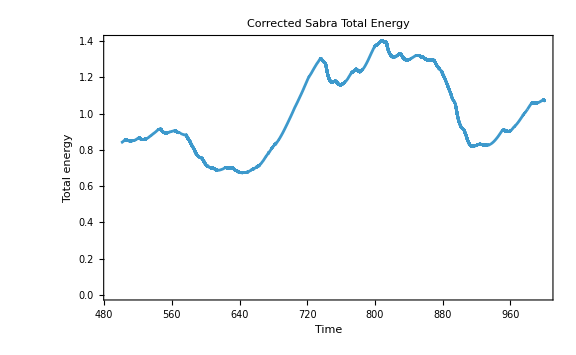

```mathematica
sabraV2Times=sabraCoreV2["Times"];

sabraV2Energy=sabraCoreV2["TotalEnergy"];

sabraV2Injection=sabraCoreV2["InstantaneousEnergyInjection"];

sabraV2Dissipation=sabraCoreV2["TotalDissipation"];

sabraV2SampleDuration=Last[sabraV2Times]-First[sabraV2Times];

sabraV2HalfLength=Floor[Length[sabraV2Energy]/2];


sabraV2FirstHalfEnergy=Take[sabraV2Energy,sabraV2HalfLength];

sabraV2SecondHalfEnergy=Take[sabraV2Energy,-sabraV2HalfLength];


sabraV2StationaritySummary=<|"InitialEnergy"->First[sabraV2Energy],"FinalEnergy"->Last[sabraV2Energy],"MeanEnergy"->Mean[sabraV2Energy],"RelativeNetEnergyChange"->(Last[sabraV2Energy]-First[sabraV2Energy])/Mean[sabraV2Energy],"FirstHalfMeanEnergy"->Mean[sabraV2FirstHalfEnergy],"SecondHalfMeanEnergy"->Mean[sabraV2SecondHalfEnergy],"RelativeHalfMeanShift"->(Mean[sabraV2SecondHalfEnergy]-Mean[sabraV2FirstHalfEnergy])/Mean[sabraV2Energy],"MeanInjectionFromLedger"->Re[sabraCoreV2["EnergyLedger"]["IntegratedInjection"]]/sabraV2SampleDuration,"MeanDissipationFromLedger"->Re[sabraCoreV2["EnergyLedger"]["IntegratedDissipation"]]/sabraV2SampleDuration,"DissipationToInjectionRatio"->Re[sabraCoreV2["EnergyLedger"]["IntegratedDissipation"]/sabraCoreV2["EnergyLedger"]["IntegratedInjection"]],"RelativeLedgerResidual"->sabraCoreV2["EnergyLedger"]["RelativeLedgerResidual"]|>;


Dataset[sabraV2StationaritySummary]
sabraV2SmoothingDuration=20.;

sabraV2SmoothingLength=Max[2,Round[sabraV2SmoothingDuration/sabraCoreV2["Parameters"]["SampleInterval"]]];

sabraV2SmoothedTimes=Drop[sabraV2Times,sabraV2SmoothingLength-1];


sabraV2EnergyPlot=ListLinePlot[Transpose[{sabraV2Times,sabraV2Energy}],Frame->True,FrameLabel->{"Time","Total energy"},PlotLabel->"Corrected Sabra Total Energy",PlotRange->All,ImageSize->Large];


sabraV2PowerPlot=ListLinePlot[{Transpose[{sabraV2SmoothedTimes,MovingAverage[sabraV2Injection,sabraV2SmoothingLength]}],Transpose[{sabraV2SmoothedTimes,MovingAverage[sabraV2Dissipation,sabraV2SmoothingLength]}]},PlotLegends->{"Mean injected power","Mean dissipation"},Frame->True,FrameLabel->{"Time","Power"},PlotLabel->"Running Energy Injection and Dissipation",PlotRange->All,ImageSize->Large];
GraphicsColumn[{sabraV2EnergyPlot,sabraV2PowerPlot}]
```

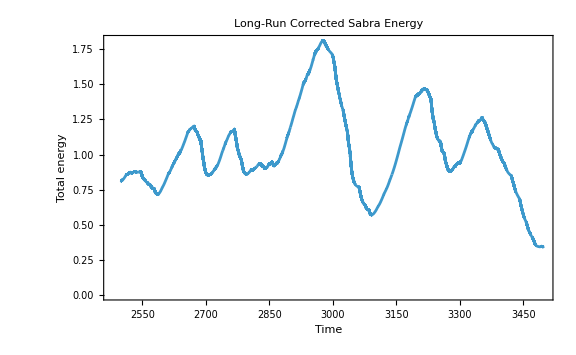

```mathematica
sabraCoreV2Long=GenerateSabraTurbulenceV2[20260817,"BurnInTime"->2500.,"SampleDuration"->1000.,"SampleInterval"->0.01,"MaximumStepSize"->0.01];
sabraLongTimes=sabraCoreV2Long["Times"];
sabraLongEnergy=sabraCoreV2Long["TotalEnergy"];
sabraLongBlockCount=4;
sabraLongBlockLength=Floor[Length[sabraLongEnergy]/sabraLongBlockCount];
sabraLongEnergyBlocks=Partition[Take[sabraLongEnergy,sabraLongBlockCount*sabraLongBlockLength],sabraLongBlockLength];
sabraLongBlockMeans=Mean/@sabraLongEnergyBlocks;
sabraLongMeanEnergy=Mean[sabraLongEnergy];
sabraLongSampleDuration=Last[sabraLongTimes]-First[sabraLongTimes];
sabraLongStationaritySummary=<|"EnergyBlockMeans"->sabraLongBlockMeans,"MaximumRelativeBlockDeviation"->Max[Abs[sabraLongBlockMeans-sabraLongMeanEnergy]]/sabraLongMeanEnergy,"RelativeNetEnergyChange"->(Last[sabraLongEnergy]-First[sabraLongEnergy])/sabraLongMeanEnergy,"MeanInjectionFromLedger"->Re[sabraCoreV2Long["EnergyLedger"]["IntegratedInjection"]]/sabraLongSampleDuration,"MeanDissipationFromLedger"->Re[sabraCoreV2Long["EnergyLedger"]["IntegratedDissipation"]]/sabraLongSampleDuration,"DissipationToInjectionRatio"->Re[sabraCoreV2Long["EnergyLedger"]["IntegratedDissipation"]/sabraCoreV2Long["EnergyLedger"]["IntegratedInjection"]],"RelativeLedgerResidual"->sabraCoreV2Long["EnergyLedger"]["RelativeLedgerResidual"]|>;
Dataset[sabraLongStationaritySummary]
ListLinePlot[Transpose[{sabraLongTimes,sabraLongEnergy}],Frame->True,FrameLabel->{"Time","Total energy"},PlotLabel->"Long-Run Corrected Sabra Energy",PlotRange->All,ImageSize->Large]
```

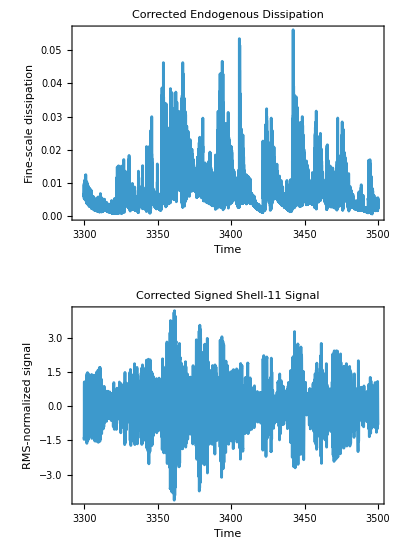

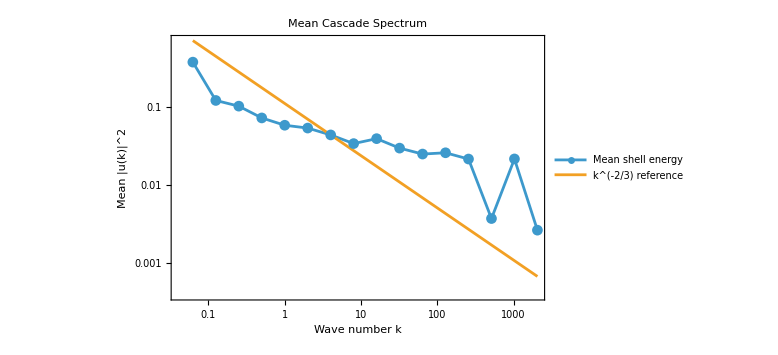

```mathematica
sabraLongDisplayCount=Min[20000,Length[sabraCoreV2Long["Times"]]];

sabraLongDisplayTimes=Take[sabraCoreV2Long["Times"],-sabraLongDisplayCount];


sabraLongDissipationPlot=ListLinePlot[Transpose[{sabraLongDisplayTimes,Take[sabraCoreV2Long["TotalDissipation"],-sabraLongDisplayCount]}],Frame->True,FrameLabel->{"Time","Fine-scale dissipation"},PlotLabel->"Corrected Endogenous Dissipation",PlotRange->All,ImageSize->Large];


sabraLongSignalPlot=ListLinePlot[Transpose[{sabraLongDisplayTimes,Take[sabraCoreV2Long["SignedTurbulentSignal"],-sabraLongDisplayCount]}],Frame->True,FrameLabel->{"Time","RMS-normalized signal"},PlotLabel->Row[{"Corrected Signed Shell-",sabraCoreV2Long["ObservableShell"]," Signal"}],PlotRange->All,ImageSize->Large];


GraphicsColumn[{sabraLongDissipationPlot,sabraLongSignalPlot}]
sabraLongMeanShellEnergy=Mean/@Transpose[sabraCoreV2Long["ShellEnergy"]];

sabraLongWaveNumbers=sabraCoreV2Long["WaveNumbers"];


sabraReferenceShell=7;

sabraKolmogorovReference=sabraLongMeanShellEnergy[[sabraReferenceShell]]*(sabraLongWaveNumbers/sabraLongWaveNumbers[[sabraReferenceShell]])^(-2./3.);


sabraEnergySpectrumPlot=ListLogLogPlot[{Transpose[{sabraLongWaveNumbers,sabraLongMeanShellEnergy}],Transpose[{sabraLongWaveNumbers,sabraKolmogorovReference}]},Joined->True,PlotMarkers->{Automatic,None},PlotLegends->{"Mean shell energy","k^(-2/3) reference"},Frame->True,FrameLabel->{"Wave number k","Mean |u(k)|^2"},PlotLabel->"Mean Cascade Spectrum",PlotRange->All,ImageSize->Large];


sabraEnergySpectrumPlot
```

```mathematica
ClearAll[BuildGeneralTurbulence1D];
Options[BuildGeneralTurbulence1D]={"ObservationInterval"->0.1,"OutputLocation"->0.,"OutputAmplitude"->1.};
BuildGeneralTurbulence1D[cascadeCore_Association,OptionsPattern[]]:=Module[{observationInterval,outputLocation,outputAmplitude,integrationInterval,observationStride,observationIndices,modelTimes,signedCascadeSignal,relativeIntensity,dissipation,outputValues},observationInterval=N@OptionValue["ObservationInterval"];
outputLocation=N@OptionValue["OutputLocation"];
outputAmplitude=N@OptionValue["OutputAmplitude"];
integrationInterval=cascadeCore["Parameters"]["SampleInterval"];
observationStride=Max[1,Round[observationInterval/integrationInterval]];
observationIndices=Range[1,Length[cascadeCore["Times"]],observationStride];
modelTimes=cascadeCore["Times"][[observationIndices]];
signedCascadeSignal=cascadeCore["SignedTurbulentSignal"][[observationIndices]];
relativeIntensity=cascadeCore["ConditionalScale"][[observationIndices]];
dissipation=cascadeCore["TotalDissipation"][[observationIndices]];
outputValues=outputLocation+outputAmplitude signedCascadeSignal;
<|"Stage"->"GeneralOneDimensionalTurbulence","SourceStage"->cascadeCore["Stage"],"Seed"->cascadeCore["Seed"],"Times"->modelTimes,"Values"->outputValues,"SignedCascadeSignal"->signedCascadeSignal,"RelativeIntensity"->relativeIntensity,"Dissipation"->dissipation,"ObservationParameters"-><|"ObservationInterval"->observationInterval,"IntegrationInterval"->integrationInterval,"ObservationStride"->observationStride,"OutputLocation"->outputLocation,"OutputAmplitude"->outputAmplitude|>,"Construction"-><|"AdditionalRandomness"->False,"ExplicitPeakProcess"->False,"ExplicitSeverityDistribution"->False,"ThresholdReleaseMechanism"->False,"PeakOrigin"->"Endogenous nonlinear interscale transfer"|>|>];
generalTurbulence1D=BuildGeneralTurbulence1D[sabraCoreV2Long,"ObservationInterval"->0.1];
Dataset[generalTurbulence1D["Construction"]]
```

```mathematica
(*Market adapter*)
ClearAll[SabraMarketAdapter];


Options[SabraMarketAdapter]={"InitialPrice"->100.,"AnnualizedLogDrift"->0.,"AnnualizedVolatilityScale"->0.20,"PeriodsPerYear"->252.};


SabraMarketAdapter[turbulence1D_Association,OptionsPattern[]]:=Module[{initialPrice,annualizedLogDrift,annualizedVolatilityScale,periodsPerYear,periodDrift,periodScale,turbulentCarrier,returns,prices,returnTimes,priceTimes},initialPrice=N@OptionValue["InitialPrice"];
annualizedLogDrift=N@OptionValue["AnnualizedLogDrift"];
annualizedVolatilityScale=N@OptionValue["AnnualizedVolatilityScale"];
periodsPerYear=N@OptionValue["PeriodsPerYear"];
periodDrift=annualizedLogDrift/periodsPerYear;
periodScale=annualizedVolatilityScale/Sqrt[periodsPerYear];
turbulentCarrier=turbulence1D["Values"];
(*No sample-centering and no second volatility modulation*)returns=periodDrift+periodScale turbulentCarrier;
prices=initialPrice Exp[Prepend[Accumulate[returns],0.]];
returnTimes=Range[Length[returns]];
priceTimes=Range[0,Length[returns]];
<|"Stage"->"SabraMarketAdapter","Seed"->turbulence1D["Seed"],"Returns"->returns,"Prices"->prices,"ReturnTimes"->returnTimes,"PriceTimes"->priceTimes,"RelativeIntensity"->turbulence1D["RelativeIntensity"],"CoreDissipation"->turbulence1D["Dissipation"],"TurbulentCarrier"->turbulentCarrier,"MarketParameters"-><|"InitialPrice"->initialPrice,"AnnualizedLogDrift"->annualizedLogDrift,"AnnualizedVolatilityScale"->annualizedVolatilityScale,"PeriodsPerYear"->periodsPerYear,"PeriodScale"->periodScale|>,"Construction"-><|"DynamicVolatilitySource"->"Endogenous Sabra cascade","AdditionalMarketNoise"->False,"SampleMeanRemoved"->False|>|>];
sabraMarketResult=SabraMarketAdapter[generalTurbulence1D,"InitialPrice"->100.,"AnnualizedLogDrift"->0.,"AnnualizedVolatilityScale"->0.20,"PeriodsPerYear"->252.];
```

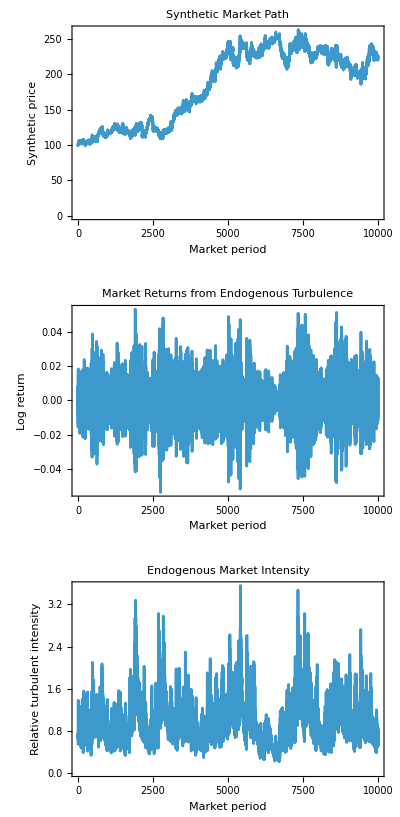

```mathematica
(*Plots*)
sabraMarketReturnPlot=ListLinePlot[Transpose[{sabraMarketResult["ReturnTimes"],sabraMarketResult["Returns"]}],Frame->True,FrameLabel->{"Market period","Log return"},PlotLabel->"Market Returns from Endogenous Turbulence",PlotRange->All,ImageSize->Large];


sabraMarketIntensityPlot=ListLinePlot[Transpose[{sabraMarketResult["ReturnTimes"],sabraMarketResult["RelativeIntensity"]}],Frame->True,FrameLabel->{"Market period","Relative turbulent intensity"},PlotLabel->"Endogenous Market Intensity",PlotRange->All,ImageSize->Large];


sabraMarketPricePlot=ListLinePlot[Transpose[{sabraMarketResult["PriceTimes"],sabraMarketResult["Prices"]}],Frame->True,FrameLabel->{"Market period","Synthetic price"},PlotLabel->"Synthetic Market Path",PlotRange->All,ImageSize->Large];


GraphicsColumn[{sabraMarketPricePlot,sabraMarketReturnPlot,sabraMarketIntensityPlot}]
```

```mathematica
ClearAll[verificationSampleACF,verificationAggregate,VerifyTurbulentMarket];
verificationSampleACF[data_List,maximumLag_Integer]:=Table[Correlation[Take[data,Length[data]-lag],Drop[data,lag]],{lag,maximumLag}];
verificationAggregate[data_List,horizon_Integer]:=Total/@Partition[data,horizon,horizon];
Options[VerifyTurbulentMarket]={"PeriodsPerYear"->252.,"TailProbabilities"->{0.001,0.01,0.05,0.50,0.95,0.99,0.999},"AggregationHorizons"->{1,2,5,10,20,60,120},"ScalingHorizons"->{1,2,4,8,16,32,64,128,256},"ScalingOrders"->Range[0.5,5.,0.5],"MaximumACFLag"->20};


VerifyTurbulentMarket[marketResult_Association,OptionsPattern[]]:=Module[{returns,observationCount,periodsPerYear,meanReturn,returnStandardDeviation,annualizedVolatility,returnSkewness,excessKurtosis,jarqueBeraStatistic,jarqueBeraPValue,standardizedReturns,tailProbabilities,tailComparison,aggregationHorizons,aggregationResults,scalingHorizons,scalingOrders,scalingResults,scalingData,scalingFit,zetaOrders,zetaValues,zetaCoefficients,zetaCurvature,maximumACFLag,returnACF,absoluteReturnACF,squaredReturnACF},returns=N@marketResult["Returns"];
observationCount=Length[returns];
periodsPerYear=N@OptionValue["PeriodsPerYear"];
meanReturn=Mean[returns];
returnStandardDeviation=StandardDeviation[returns];
annualizedVolatility=returnStandardDeviation Sqrt[periodsPerYear];
returnSkewness=Skewness[returns];
excessKurtosis=Kurtosis[returns]-3.;
jarqueBeraStatistic=observationCount/6.*(returnSkewness^2+excessKurtosis^2/4.);
jarqueBeraPValue=SurvivalFunction[ChiSquareDistribution[2],jarqueBeraStatistic];
(*Standardization is only for distribution diagnostics*)standardizedReturns=(returns-meanReturn)/returnStandardDeviation;
tailProbabilities=OptionValue["TailProbabilities"];
tailComparison=Map[<|"Probability"->#,"GeneratedQuantile"->Quantile[standardizedReturns,#],"GaussianQuantile"->Quantile[NormalDistribution[0.,1.],#]|>&,tailProbabilities];
aggregationHorizons=Select[OptionValue["AggregationHorizons"],#<=observationCount&];
aggregationResults=Table[Module[{aggregatedReturns=verificationAggregate[returns,horizon]},<|"Horizon"->horizon,"Observations"->Length[aggregatedReturns],"Skewness"->Skewness[aggregatedReturns],"ExcessKurtosis"->Kurtosis[aggregatedReturns]-3.|>],{horizon,aggregationHorizons}];
scalingHorizons=Select[OptionValue["ScalingHorizons"],#<=Floor[observationCount/20]&];
scalingOrders=OptionValue["ScalingOrders"];
scalingResults=Table[scalingData=Table[Module[{increments=Total/@Partition[returns,horizon,1]},{Log[N[horizon]],Log[Mean[Abs[increments]^order]]}],{horizon,scalingHorizons}];
scalingFit=LinearModelFit[scalingData,scaleVariable,scaleVariable];
<|"Order"->order,"Zeta"->N[scaleVariable/.
scalingFit["BestFitParameters"]],"RSquared"->N[scalingFit["RSquared"]]|>,{order,scalingOrders}];
zetaOrders=scalingResults[[All,"Order"]];
zetaValues=scalingResults[[All,"Zeta"]];
zetaCoefficients=LeastSquares[({1.,#,#^2})&/@zetaOrders,zetaValues];
zetaCurvature=zetaCoefficients[[3]];
maximumACFLag=OptionValue["MaximumACFLag"];
returnACF=verificationSampleACF[returns,maximumACFLag];
absoluteReturnACF=verificationSampleACF[Abs[returns],maximumACFLag];
squaredReturnACF=verificationSampleACF[returns^2,maximumACFLag];
<|"Distribution"-><|"Observations"->observationCount,"MeanReturn"->meanReturn,"AnnualizedVolatility"->annualizedVolatility,"Skewness"->returnSkewness,"ExcessKurtosis"->excessKurtosis,"JarqueBeraStatistic"->jarqueBeraStatistic,"JarqueBeraPValue"->jarqueBeraPValue|>,"TailComparison"->tailComparison,"Aggregation"->aggregationResults,"ScalingExponents"->scalingResults,"ZetaCurvature"->zetaCurvature,"ReturnACF"->returnACF,"AbsoluteReturnACF"->absoluteReturnACF,"SquaredReturnACF"->squaredReturnACF,"MaximumAbsoluteReturnACFFirst20Lags"->Max[Abs[returnACF]],"MeanAbsoluteReturnACFFirst20Lags"->Mean[absoluteReturnACF],"MeanSquaredReturnACFFirst20Lags"->Mean[squaredReturnACF]|>];
sabraVerification=VerifyTurbulentMarket[sabraMarketResult];
Dataset[sabraVerification]
Dataset[sabraVerification["TailComparison"]]
Dataset[sabraVerification["Aggregation"]]
Dataset[sabraVerification["ScalingExponents"]]
```

ReplaceAll::reps: {-2.48607,0.166383} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.

ReplaceAll::reps: {-4.76929,0.327933} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
ClearAll[CorrectScalingExponents];


CorrectScalingExponents[returns_List,scalingHorizons_List,scalingOrders_List]:=Table[Module[{scalingData,logHorizons,logMoments,designMatrix,coefficients,fittedValues,residualSumSquares,totalSumSquares,rSquared},scalingData=Table[Module[{aggregatedIncrements=Total/@Partition[returns,horizon,1]},{Log[N[horizon]],Log[Mean[Abs[aggregatedIncrements]^order]]}],{horizon,scalingHorizons}];
logHorizons=scalingData[[All,1]];
logMoments=scalingData[[All,2]];
designMatrix=Transpose[{ConstantArray[1.,Length[logHorizons]],logHorizons}];
coefficients=LeastSquares[designMatrix,logMoments];
fittedValues=designMatrix.coefficients;
residualSumSquares=Total[(logMoments-fittedValues)^2];
totalSumSquares=Total[(logMoments-Mean[logMoments])^2];
rSquared=If[totalSumSquares>0.,1.-residualSumSquares/totalSumSquares,1.];
<|"Order"->order,"Zeta"->coefficients[[2]],"RSquared"->rSquared|>],{order,scalingOrders}];
sabraCorrectedScalingExponents=CorrectScalingExponents[sabraMarketResult["Returns"],{1,2,4,8,16,32,64,128,256},Range[0.5,5.,0.5]];


sabraCorrectedZetaOrders=Lookup[sabraCorrectedScalingExponents,"Order"];

sabraCorrectedZetaValues=Lookup[sabraCorrectedScalingExponents,"Zeta"];


sabraCorrectedZetaCoefficients=LeastSquares[({1.,#,#^2})&/@sabraCorrectedZetaOrders,sabraCorrectedZetaValues];


sabraCorrectedZetaCurvature=sabraCorrectedZetaCoefficients[[3]];


sabraVerification=Join[sabraVerification,<|"ScalingExponents"->sabraCorrectedScalingExponents,"ZetaCurvature"->sabraCorrectedZetaCurvature|>];


Dataset[sabraVerification["ScalingExponents"]]

sabraVerification["ZetaCurvature"]
sabraObservationIntervalCandidates=Range[0.05,1.00,0.05];


sabraObservationIntervalScan=Table[Module[{candidateOutput,candidateSignal,candidateReturnACF,candidateAbsoluteACF,candidateSquaredACF},candidateOutput=BuildGeneralTurbulence1D[sabraCoreV2Long,"ObservationInterval"->observationInterval];
candidateSignal=candidateOutput["Values"];
candidateReturnACF=verificationSampleACF[candidateSignal,20];
candidateAbsoluteACF=verificationSampleACF[Abs[candidateSignal],20];
candidateSquaredACF=verificationSampleACF[candidateSignal^2,20];
<|"ObservationInterval"->observationInterval,"Observations"->Length[candidateSignal],"MaximumAbsoluteRawACF"->Max[Abs[candidateReturnACF]],"MeanAbsoluteReturnACF"->Mean[candidateAbsoluteACF],"MeanSquaredReturnACF"->Mean[candidateSquaredACF],"ExcessKurtosis"->Kurtosis[candidateSignal]-3.|>],{observationInterval,sabraObservationIntervalCandidates}];
sabraEligibleObservationIntervals=Select[sabraObservationIntervalScan,#["Observations"]>=2000&];


sabraRankedObservationIntervals=SortBy[sabraEligibleObservationIntervals,#["MaximumAbsoluteRawACF"]&];


Dataset[Take[sabraRankedObservationIntervals,UpTo[10]]]
```

-0.00824832

```mathematica
sabraCoreFinal=GenerateSabraTurbulenceV2[20260817,"BurnInTime"->2500.,"SampleDuration"->2500.,"SampleInterval"->0.03,"MaximumStepSize"->0.01];
generalTurbulence1DFinal=BuildGeneralTurbulence1D[sabraCoreFinal,"ObservationInterval"->0.30];
Length[generalTurbulence1DFinal["Values"]]
sabraMarketResultFinal=SabraMarketAdapter[generalTurbulence1DFinal,"InitialPrice"->100.,"AnnualizedLogDrift"->0.,"AnnualizedVolatilityScale"->0.20,"PeriodsPerYear"->252.];
ClearAll[VerifyTurbulentMarketV2];


VerifyTurbulentMarketV2[marketResult_Association]:=Module[{result,returns,observationCount,scalingHorizons,scalingOrders,scalingExponents,zetaOrders,zetaValues,zetaCoefficients},result=VerifyTurbulentMarket[marketResult];
returns=marketResult["Returns"];
observationCount=Length[returns];
scalingHorizons=Select[{1,2,4,8,16,32,64,128,256},#<=Floor[observationCount/20]&];
scalingOrders=Range[0.5,5.,0.5];
scalingExponents=CorrectScalingExponents[returns,scalingHorizons,scalingOrders];
zetaOrders=Lookup[scalingExponents,"Order"];
zetaValues=Lookup[scalingExponents,"Zeta"];
zetaCoefficients=LeastSquares[({1.,#,#^2})&/@zetaOrders,zetaValues];
Join[result,<|"ScalingExponents"->scalingExponents,"ZetaCurvature"->zetaCoefficients[[3]]|>]];
sabraVerificationFinal=VerifyTurbulentMarketV2[sabraMarketResultFinal];
Dataset[sabraVerificationFinal]
```

8334

ReplaceAll::reps: {-2.52373,0.23481} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.

ReplaceAll::reps: {-4.79019,0.480889} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(* ================================================*)(*Export final figures for README*)(* ================================================*)ClearAll["readmeExport`*"];


readmeExport`notebookDirectory=Quiet[Check[NotebookDirectory[],Directory[]]];
If[!StringQ[readmeExport`notebookDirectory],readmeExport`notebookDirectory=Directory[]];
readmeExport`directory=FileNameJoin[{readmeExport`notebookDirectory,"readme-assets"}];
If[!DirectoryQ[readmeExport`directory],CreateDirectory[readmeExport`directory,CreateIntermediateDirectories->True]];
readmeExport`coreTimes=sabraCoreFinal["Times"];

readmeExport`displayCount=Min[Length[readmeExport`coreTimes],Round[200./sabraCoreFinal["Parameters"]["SampleInterval"]]+1];

readmeExport`displayTimes=Take[readmeExport`coreTimes,-readmeExport`displayCount];
readmeExport`energyPlot=ListLinePlot[Transpose[{sabraCoreFinal["Times"],sabraCoreFinal["TotalEnergy"]}],Frame->True,FrameLabel->{"Model time","Total energy"},PlotLabel->"Bounded Large-Scale Energy",PlotRange->All,ImageSize->1400];


readmeExport`dissipationPlot=ListLinePlot[Transpose[{readmeExport`displayTimes,Take[sabraCoreFinal["TotalDissipation"],-readmeExport`displayCount]}],Frame->True,FrameLabel->{"Model time","Fine-scale dissipation"},PlotLabel->"Endogenous Intermittent Dissipation",PlotRange->All,ImageSize->1400];


readmeExport`signedSignalPlot=ListLinePlot[Transpose[{readmeExport`displayTimes,Take[sabraCoreFinal["SignedTurbulentSignal"],-readmeExport`displayCount]}],Frame->True,FrameLabel->{"Model time","RMS-normalized signal"},PlotLabel->Row[{"Signed Shell-",sabraCoreFinal["ObservableShell"]," Turbulent Signal"}],PlotRange->All,ImageSize->1400];
readmeExport`waveNumbers=sabraCoreFinal["WaveNumbers"];

readmeExport`meanShellEnergy=Mean/@Transpose[sabraCoreFinal["ShellEnergy"]];

readmeExport`referenceShell=Min[7,Length[readmeExport`waveNumbers]];

readmeExport`kolmogorovReference=readmeExport`meanShellEnergy[[readmeExport`referenceShell]]*(readmeExport`waveNumbers/readmeExport`waveNumbers[[readmeExport`referenceShell]])^(-2./3.);


readmeExport`spectrumPlot=ListLogLogPlot[{Transpose[{readmeExport`waveNumbers,readmeExport`meanShellEnergy}],Transpose[{readmeExport`waveNumbers,readmeExport`kolmogorovReference}]},Joined->True,PlotMarkers->{Automatic,None},PlotLegends->{"Mean shell energy","k^(-2/3) reference"},Frame->True,FrameLabel->{"Wave number k","Mean |u(k)|^2"},PlotLabel->"Mean Cascade Spectrum",PlotRange->All,ImageSize->1400];
readmeExport`pricePlot=ListLinePlot[Transpose[{sabraMarketResultFinal["PriceTimes"],sabraMarketResultFinal["Prices"]}],Frame->True,FrameLabel->{"Market period","Synthetic price"},PlotLabel->"Synthetic Market Path",PlotRange->All,ImageSize->1400];


readmeExport`returnPlot=ListLinePlot[Transpose[{sabraMarketResultFinal["ReturnTimes"],sabraMarketResultFinal["Returns"]}],Frame->True,FrameLabel->{"Market period","Log return"},PlotLabel->"Returns from Endogenous Turbulence",PlotRange->All,ImageSize->1400];


readmeExport`intensityPlot=ListLinePlot[Transpose[{sabraMarketResultFinal["ReturnTimes"],sabraMarketResultFinal["RelativeIntensity"]}],Frame->True,FrameLabel->{"Market period","Relative turbulent intensity"},PlotLabel->"Endogenous Market Intensity",PlotRange->All,ImageSize->1400];
readmeExport`tailData=sabraVerificationFinal["TailComparison"];

readmeExport`generatedQuantiles=Lookup[readmeExport`tailData,"GeneratedQuantile"];

readmeExport`gaussianQuantiles=Lookup[readmeExport`tailData,"GaussianQuantile"];

readmeExport`tailRange=MinMax[Join[readmeExport`generatedQuantiles,readmeExport`gaussianQuantiles]];


readmeExport`tailPlot=ListPlot[Transpose[{readmeExport`gaussianQuantiles,readmeExport`generatedQuantiles}],PlotMarkers->Automatic,Epilog->{Gray,Dashed,Line[{{readmeExport`tailRange[[1]],readmeExport`tailRange[[1]]},{readmeExport`tailRange[[2]],readmeExport`tailRange[[2]]}}]},Frame->True,FrameLabel->{"Gaussian quantile","Generated quantile"},PlotLabel->"Tail Quantiles versus Gaussian",PlotRange->All,ImageSize->1400];
readmeExport`aggregationData=sabraVerificationFinal["Aggregation"];


readmeExport`aggregationPlot=ListLinePlot[Transpose[{Lookup[readmeExport`aggregationData,"Horizon"],Lookup[readmeExport`aggregationData,"ExcessKurtosis"]}],PlotMarkers->Automatic,Frame->True,FrameLabel->{"Aggregation horizon","Excess kurtosis"},PlotLabel->"Persistence of Non-Gaussian Tails",PlotRange->All,ImageSize->1400];

readmeExport`maximumACFLag=Length[sabraVerificationFinal["ReturnACF"]];


readmeExport`acfPlot=ListLinePlot[{Transpose[{Range[readmeExport`maximumACFLag],sabraVerificationFinal["ReturnACF"]}],Transpose[{Range[readmeExport`maximumACFLag],sabraVerificationFinal["AbsoluteReturnACF"]}],Transpose[{Range[readmeExport`maximumACFLag],sabraVerificationFinal["SquaredReturnACF"]}]},PlotLegends->{"Returns","Absolute returns","Squared returns"},PlotMarkers->Automatic,Frame->True,FrameLabel->{"Lag","Autocorrelation"},PlotLabel->"Return and Volatility Memory",PlotRange->All,ImageSize->1400];
readmeExport`scalingData=sabraVerificationFinal["ScalingExponents"];

readmeExport`scalingOrders=Lookup[readmeExport`scalingData,"Order"];

readmeExport`scalingValues=Lookup[readmeExport`scalingData,"Zeta"];


readmeExport`linearScalingCoefficients=LeastSquares[Transpose[{ConstantArray[1.,Length[readmeExport`scalingOrders]],readmeExport`scalingOrders}],readmeExport`scalingValues];


readmeExport`linearScalingReference=readmeExport`linearScalingCoefficients[[1]]+readmeExport`linearScalingCoefficients[[2]]*readmeExport`scalingOrders;


readmeExport`scalingPlot=ListLinePlot[{Transpose[{readmeExport`scalingOrders,readmeExport`scalingValues}],Transpose[{readmeExport`scalingOrders,readmeExport`linearScalingReference}]},PlotMarkers->{Automatic,None},PlotLegends->{"Measured scaling","Linear reference"},Frame->True,FrameLabel->{"Moment order q","Scaling exponent ζ(q)"},PlotLabel->Row[{"Nonlinear Scaling, curvature = ",NumberForm[sabraVerificationFinal["ZetaCurvature"],{5,4}]}],PlotRange->All,ImageSize->1400];
readmeExport`coreOverview=GraphicsGrid[{{readmeExport`energyPlot,readmeExport`dissipationPlot},{readmeExport`signedSignalPlot,readmeExport`spectrumPlot}},ImageSize->1800,Spacings->{0.4,0.5}];


readmeExport`marketOverview=GraphicsGrid[{{readmeExport`pricePlot,readmeExport`returnPlot},{readmeExport`intensityPlot,readmeExport`acfPlot}},ImageSize->1800,Spacings->{0.4,0.5}];


readmeExport`verificationOverview=GraphicsGrid[{{readmeExport`tailPlot,readmeExport`aggregationPlot},{readmeExport`acfPlot,readmeExport`scalingPlot}},ImageSize->1800,Spacings->{0.4,0.5}];
readmeExport`graphics=<|"turbulence-energy.png"->readmeExport`energyPlot,"turbulence-dissipation.png"->readmeExport`dissipationPlot,"turbulence-signed-signal.png"->readmeExport`signedSignalPlot,"turbulence-spectrum.png"->readmeExport`spectrumPlot,"market-price-path.png"->readmeExport`pricePlot,"market-returns.png"->readmeExport`returnPlot,"market-intensity.png"->readmeExport`intensityPlot,"verification-tail-quantiles.png"->readmeExport`tailPlot,"verification-aggregation.png"->readmeExport`aggregationPlot,"verification-autocorrelation.png"->readmeExport`acfPlot,"verification-scaling.png"->readmeExport`scalingPlot,"turbulence-core-overview.png"->readmeExport`coreOverview,"market-overview.png"->readmeExport`marketOverview,"verification-overview.png"->readmeExport`verificationOverview|>;


readmeExport`exportedFiles=Association@KeyValueMap[Function[{fileName,graphic},fileName->Export[FileNameJoin[{readmeExport`directory,fileName}],graphic,"PNG",ImageResolution->220]],readmeExport`graphics];


Dataset[readmeExport`exportedFiles]
```